```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

```mathematica
(*K=k/(d/(1-2 θ/π))*)
```

```mathematica
(*k = K d/(1-2 θ/π)*)
```

```mathematica
df[ζ_]=K (1+d^2/ζ^2)^(θ/π);
f[ζ_]=c+ K d/(1-2 θ/π)(ζ/d)^(1-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-ζ^2/d^2];
```

```mathematica
(* Condition for d: Re@f[L]=L when L->∞ *)
Limit[(Re@f[L])/L,L->∞](*==1*)
```

Re[K]

```mathematica
(*d= K  d/1 ;->K=1*)
```

```mathematica
K=1;
```

```mathematica
(* 
dz: height hinge to y=0
du: height y=0 to horizontal mirror
du+dz = flap height.
*)
```

```mathematica
c=-(dz+du) Tan[θ]+ⅈ du;
d= √π((dz-ⅈ c) ⅇ^(-ⅈ θ))/(Gamma[1+θ/π] Gamma[1/2-θ/π]);
```

(ⅇ^(-ⅈ θ) √π (dz-ⅈ (ⅈ du+(-du-dz) Tan[θ])))/(Gamma[1/2-θ/π] Gamma[1+θ/π])

```mathematica
(* Check that the hinge position is correct: *)
Block[{dz=.6,du = .0,θ =20*π/180},{f[.00001],f[-ⅈ d+.000001]}]
```

{-0.218238+1.38916×10^-21 ⅈ,2.21622×10^-7-0.6 ⅈ}

```mathematica
(* Check that the map does not move far away from the wavemaker: *)
```

```mathematica
Block[{dz=.6,du = .0},{f[20]/.θ ->20*π/180,f[20]/.θ ->-20*π/180}]
```

{19.9985+2.79901×10^-15 ⅈ,20.0029-2.97357×10^-15 ⅈ}

```mathematica
(* Check that f and df are consistent: *)
Block[{dz=.6,du = .0,θ =20*π/180},  {df[.4-.34ⅈ],f'[.4-.34ⅈ]}]
```

{1.04439+0.0816258 ⅈ,1.04439+0.0816258 ⅈ}

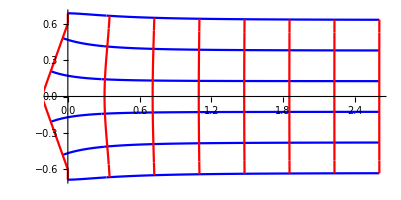

```mathematica
Block[{dz=.6,du = .0,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

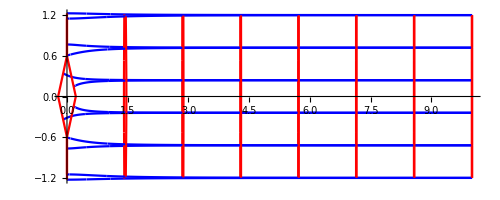

```mathematica
Show[Block[{dz=.6,du = .0,θ =20*π/180,lim={.00001,10,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]],
Block[{dz=.6,du = .0,θ =-20*π/180,lim={.00001,10,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]]
```